```mathematica
temptimelist=Range[200]/10;
tempvaluelist=Sinc[temptimelist]+RandomReal[{-0.02,0.02},200];
originalData=Transpose[{temptimelist,tempvaluelist}];
Manipulate[nearestFunction=Mean@Nearest[Thread[originalData[[All,1]]->originalData[[All,2]]],#,a]&;
(*nearest function that averages over "a" closest points*)newdata={N@#,Sequence@@(nearestFunction@#)}&/@Range[Min@originalData[[All,1]],Max@originalData[[All,1]],((Max@originalData[[All,1]]-Min@originalData[[All,1]])/Length@originalData[[All,1]]) b];
(*nearest function applied to an undersampling of your data.b=10 means a tenth of data used etc*)ListPlot[{originalData,newdata},PlotRange->All,PlotStyle->{Directive[PointSize[0.005],Blue,PlotJoined->True],Directive[PointSize[0.014],Red]}],{a,1,10,1},{b,1,20,1}]
```

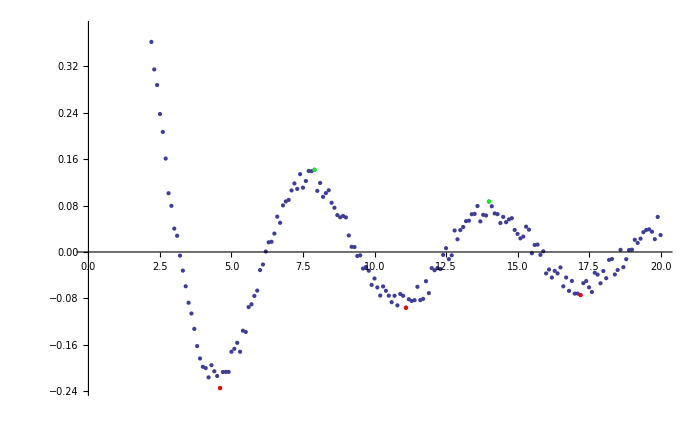

```mathematica
ClearAll[findExtrema];
findExtrema[points_List,fitOrder_Integer,around_Integer: 5]:=Module[{fit,fn,extrema,x,signs,extPoints},fit=LinearModelFit[points,x^Range[0,fitOrder],x];
fn=fit["Function"];
extrema=NSolve[fn'[x]==0,x,Reals];
signs=Sign[fn''[x]/.extrema];
extPoints=MapThread[First@SortBy[Nearest[points,#,around],#2]&,{{x,fn[x]}/.extrema,signs/.{1->Last,-1->(-Last[#]&)}}];
Map[Pick[extPoints,signs,#]&,{1,-1}]];
ClearAll[displayPoints]
displayPoints[pts_,extr_]:=ListPlot[pts,Epilog->{PointSize[Medium],Red,Point[First@extr],Green,Point[Last@extr]},ImageSize->700]
displayPoints[#,findExtrema[#,10,10]]&[Transpose[{temptimelist,tempvaluelist}]]
```

```mathematica
img1=-Graphics-;
img2=-Graphics-;
(*preprocess images*)
images={DeleteSmallComponents@Binarize[img1,.2],DeleteSmallComponents@Binarize[img2,.2]};
(*find matching points*)
matches=ImageCorrespondingPoints[images[[1]],images[[2]],"Transformation"->"Translation"];
(*Show points on images*)
MapThread[Show[#1,Graphics[{Cyan,MapIndexed[Inset[#2[[1]],#1]&,#2]}]]&,{images,matches}]
images={DeleteSmallComponents@Binarize[FillingTransform@img1,.2],DeleteSmallComponents@Binarize[FillingTransform@img2,.2]};
matches=ImageCorrespondingPoints[images[[1]],images[[2]],"Transformation"->"Similarity"]
Show[ImageAssemble[images],Graphics[{Red,PointSize[.02],MapThread[If[#2===Missing[],{Cyan,Point[#1]},Arrow[{#1,#2+{ImageDimensions[img1][[1]],0}}]]&,matches]}]]
{i1,i2}=Erosion[DeleteSmallComponents[ChanVeseBinarize[#,TargetColor->Gray]],10]&/@{img1,img2}
c1=1/.ComponentMeasurements[i1,"MinimalBoundingBox"];
c2=1/.ComponentMeasurements[i2,"MinimalBoundingBox"];
Show[ImageCompose[img1,{img2,.5}],Graphics[{Opacity[0.5],White,Polygon[c1],Polygon[c2],Green,Text[#,#]&/@c1,Text[#,#]&/@c2}]]
```

{-Graphics-,-Graphics-}

{{{353.43,359.493},{377.258,359.066}},{{503.413,375.665},{523.788,374.315}}}

-Graphics-

{-Graphics-,-Graphics-}

-Graphics-

ChanVeseBinarize::imginv: Expecting an image instead of image1.

DeleteSmallComponents::arg1: Expecting an image or a label matrix instead of ChanVeseBinarize[image1, TargetColor → GrayLevel[0.5]].

$Aborted

$Aborted

$Aborted

ImageCompose::imginv: Expecting an image or graphics instead of image1.

$Aborted